```mathematica
RiePrimeCnt[n_]:=Sum[PrimePi[n^(1/j)]/j,{j,1,Log[2,n]}]
LinnikApprox[n_]:=Sum[(-1)^(j+1)/j (-1)^j (1-n Sum[(-Log[n])^k/k!,{k,0,j–1}]),{j,1,Infinity}]
Table[{N[LinnikApprox[10^n]],N[LogIntegral[10^n]-Log[Log[10^n]]-EulerGamma]},{n,1,4}]//TableForm
```

$Aborted

```mathematica
LogIntegral[ 100.]-Log[Log[100.]]-EulerGamma
```

28.0217

```mathematica
-Gamma[ 0,  -Log[100.]]-Pi I-Log[Log[100]] -EulerGamma
```

28.0217+0. ⅈ

```mathematica
ff[ n_, z_, t_] := (Sum[ Binomial[z,k] (-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k]),{k,0, t}]-1)/z
ff2[ n_, z_, t_] := Sum[ Binomial[z,k] (-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k]),{k,0, t}]
```

```mathematica
N[Limit[ ff[ 100, z, 30], z->0]]
```

28.0217+9.30681×10^-27 ⅈ

```mathematica
1-Log[1000.]
```

-5.90776

```mathematica
N[Gamma[2, -Log[200]]]/200
```

-4.29832+5.26392×10^-16 ⅈ

```mathematica
ff2[100.,3,1000]
```

2081.41-3.03869×10^-13 ⅈ

```mathematica
ff2[100.,-2,2000]
```

2.39346+1.62995×10^-12 ⅈ

```mathematica
N[Gamma[3, -Log[100]]]
```

1399.73-3.42834×10^-13 ⅈ

```mathematica
ff3[ n_, z_, s_] := Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!)Integrate[ t^(k-1)E^(-t),{t,-Log[n],0}],{k,0, s}]
```

```mathematica
N[ff3[ 100, 3, 30]]
```

Integrate::idiv: Integral of ⅇ^-t/t does not converge on {-Log[100], 0}.

$Aborted

```mathematica
ff4[ n_, z_, s_] := Sum[Integrate[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{t,-Log[n],0}],{k,0, s}]
```

```mathematica
N[ff4[ 120, 3, 40]]
```

2643.2

```mathematica
ff5[ n_, z_] := Integrate[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
```

```mathematica
N[ff5[ 10, z]]
```

-1.+LaguerreL[-1. z,2.30259]

```mathematica
Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}]
```

ⅇ^-t z Hypergeometric1F1[1-z,2,t]

```mathematica
Log[10.]
```

2.30259

```mathematica
-1.+LaguerreL[-1. z,Log[10]]/.z->2
```

32.0259

```mathematica
N[Limit[ (LaguerreL[-z,Log[100]]-1)/z,z->0]]
```

28.0217

```mathematica
-1.+LaguerreL[-1,Log[10]]
```

9.

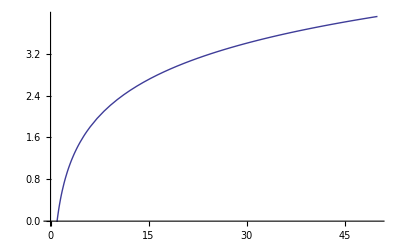

```mathematica
Plot[ Re[-1+LaguerreL[1, -Log[n]]],{n,0,50}]
```

```mathematica
N[ff2[ 1000, -2+I, 1000]]
```

27.1002+19.121 ⅈ

```mathematica
N[LaguerreL[ 2+I, Log[1000]]]
```

27.1002-19.121 ⅈ

```mathematica
N[Limit[ (LaguerreL[-z, Log[20]]-1)/z, z->0]]
```

8.2309

```mathematica
LogIntegral[ 20.]-Log[Log[20.]]-EulerGamma
```

8.2309

```mathematica
ExpIntegralEi[ZetaZero[1]Log[1000.]]
```

-0.0879017+3.45317 ⅈ

```mathematica
Limit[ N[(LaguerreL[ -z, ZetaZero[1]Log[1000]]-1)/z],z->0]+Log[ZetaZero[1] Log[1000]]+EulerGamma
```

-0.0879017+3.45317 ⅈ

```mathematica
N[E^EulerGamma]
```

1.78107

```mathematica
N[Limit[( LaguerreL[-z,Log[100]]-1)/z,z->0]]
```

28.0217

```mathematica
N[LogIntegral[100]-Log[Log[100]]-EulerGamma]
```

28.0217

```mathematica
Sum[ N[D[ LaguerreL[ -z, Log[10]],{z,k}]/.z->0]/k!,{k,0,5}]
```

9.99914

```mathematica
Sum[ N[D[ LaguerreL[ -z, Log[10]],{z,k}]/.z->0]/k!,{k,0,6}]
```

9.99996

```mathematica
N[D[( LaguerreL[-z,Log[100]]-1)/z,z]]
```

28.0217

```mathematica
N[-Pi I - Gamma[ 0, -Log[100]]]
```

30.1261+0. ⅈ

```mathematica
LogIntegral[100.]
```

30.1261

```mathematica
Limit[(LaguerreL[-ee,Log[100.]]-1)/ee,ee->0]
```

28.0217

```mathematica
N[Limit[( LaguerreL[-z,Log[100]]-1)/z,z->0]]
```

28.0217

```mathematica
N[D[LaguerreL[-z,Log[100]],z]]/.z->0
```

28.0217

```mathematica
D[ LaguerreL[-z,Log[100.]],{z,2}]/.z->0
```

80.5038

```mathematica
P2[n_,0]:=1
P2[n_,k_]:=P2[n,k]=Sum[FullSimplify[MangoldtLambda[j]/Log[j]] P2[n/j,k-1],{j,2,Floor[n]}]
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,Floor[n]}];D2[n_,0]:=1
D1[n_,z_]:=Sum[Binomial[z,k] D2[n,k],{k,0,Log[2,n]}]
```

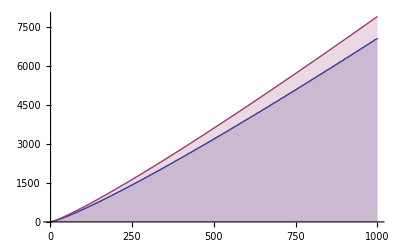

```mathematica
DiscretePlot[{ D1[n,2], LaguerreL[-2,Log[n]]}, {n,1,1000}]
```

```mathematica
Integrate[ 1/Log[x],{x,1.1,n},PrincipalValue->True]
```

ConditionalExpression[1.67577+LogIntegral[n],Im[n]≠0||Re[n]≥1.]

```mathematica
TestSum[ n_, z_, t_] := Sum[ N[Binomial[z,k] (-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k])],{k,0, t}]
Grid[ Table[ { Re[TestSum[n, k,23]], N[LaguerreL[-k, Log[n]]]}, {n,10, 100, 10},{k,-5,5}]]
```

{0.966672,0.966672} | {0.727895,0.727895} | {0.0104133,0.0104133} | {-0.954221,-0.954221} | {-1.30259,-1.30259} | {1.,1.} | {10.,10.} | {33.0259,33.0259} | {82.5612,82.5612} | {178.953,178.953} | {354.26,354.26}
{0.853716,0.853716} | {1.37285,1.37285} | {0.993598,0.993598} | {-0.504259,-0.504259} | {-1.99573,-1.99573} | {1.,1.} | {20.,20.} | {79.9146,79.9146} | {229.573,229.573} | {558.593,558.593} | {1223.71,1223.71}
{0.345442,0.345447} | {1.4452,1.4452} | {1.59103,1.59103} | {-0.018323,-0.0183229} | {-2.4012,-2.4012} | {1.,1.} | {30.,30.} | {132.036,132.036} | {407.594,407.594} | {1053.4,1053.4} | {2433.46,2433.46}
{-0.182647,-0.182608} | {1.31842,1.31842} | {1.97883,1.97883} | {0.426157,0.426157} | {-2.68888,-2.68888} | {1.,1.} | {40.,40.} | {187.555,187.555} | {607.267,607.267} | {1633.79,1633.79} | {3910.39,3910.39}
{-0.66439,-0.664191} | {1.10954,1.10957} | {2.2416,2.2416} | {0.827916,0.827916} | {-2.91202,-2.91202} | {1.,1.} | {50.,50.} | {245.601,245.601} | {823.8,823.8} | {2283.51,2283.51} | {5611.57,5611.57}
{-1.09019,-1.08949} | {0.865209,0.86531} | {2.42308,2.42309} | {1.19314,1.19314} | {-3.09434,-3.09434} | {1.,1.} | {60.,60.} | {305.661,305.661} | {1054.23,1054.23} | {2992.07,2992.07} | {7508.1,7508.1}
{-1.46377,-1.46181} | {0.606799,0.607082} | {2.54836,2.5484} | {1.52786,1.52787} | {-3.2485,-3.2485} | {1.,1.} | {70.,70.} | {367.395,367.395} | {1296.53,1296.53} | {3752.05,3752.05} | {9578.84,9578.84}
{-1.79198,-1.78731} | {0.344902,0.345574} | {2.63302,2.6331} | {1.83702,1.83703} | {-3.38203,-3.38203} | {1.,1.} | {80.,80.} | {430.562,430.562} | {1549.21,1549.21} | {4557.87,4557.87} | {11807.5,11807.5}
{-2.08206,-2.0722} | {0.0849608,0.0863776} | {2.68727,2.68743} | {2.12451,2.12452} | {-3.49981,-3.49981} | {1.,1.} | {90.,90.} | {494.983,494.983} | {1811.14,1811.14} | {5405.17,5405.17} | {14181.2,14181.2}
{-2.34096,-2.32202} | {-0.170259,-0.167536} | {2.71814,2.71845} | {2.39343,2.39346} | {-3.60517,-3.60517} | {1.,1.} | {100.,100.} | {560.517,560.517} | {2081.41,2081.41} | {6290.43,6290.43} | {16689.3,16689.3}

```mathematica
Table[{N[Sum[(-1)^(k+1)/k ((-1)^k(1-Gamma[k,-Log[n]]/Gamma[k])),{k,1,30}]],N[ Limit[ (LaguerreL[-z,Log[n]]-1)/z,z->0]],N[LogIntegral[n]-Log[Log[n]]-EulerGamma]},{n,100,600,100}]//TableForm
```

28.0217-2.09386×10^-14 ⅈ | 28.0217 | 28.0217
47.9476-4.32162×10^-14 ⅈ | 47.9476 | 47.9476
66.0153-1.89547×10^-13 ⅈ | 66.0153 | 66.0153
83.0503-4.70318×10^-13 ⅈ | 83.0503 | 83.0503
99.3898-1.32718×10^-12 ⅈ | 99.3898 | 99.3898
115.213-2.10999×10^-12 ⅈ | 115.213 | 115.213

```mathematica
N[ Limit[ (LaguerreL[-z,Log[600]]-1)/z,z->0]]
```

115.213

```mathematica
N[LogIntegral[600]-Log[Log[600]]-EulerGamma]
```

115.213

```mathematica
Table[{N[Sum[(-1)^(k+1)/k ((-1)^k(1-Gamma[k,-Log[n]]/Gamma[k])),{k,1,30}]],N[Limit[(LaguerreL[-z,Log[n]]-1)/z,z->0]],N[LogIntegral[n]-Log[Log[n]]-EulerGamma]},{n,100,600,100}]//TableForm
```

28.0217-2.09386×10^-14 ⅈ | 28.0217 | 28.0217
47.9476-4.32162×10^-14 ⅈ | 47.9476 | 47.9476
66.0153-1.89547×10^-13 ⅈ | 66.0153 | 66.0153
83.0503-4.70318×10^-13 ⅈ | 83.0503 | 83.0503
99.3898-1.32718×10^-12 ⅈ | 99.3898 | 99.3898
115.213-2.10999×10^-12 ⅈ | 115.213 | 115.213

```mathematica
Limit[ Sum[ c^j/j,{j,2,Log[c,100]}],c->1]
```

Limit[-c-100 c LerchPhi[c,1,1+Log[100]/Log[c]]-Log[1-c],c→1]

```mathematica
Binomial[z,0]
```

1

```mathematica
Binomial[z,1]
```

z

```mathematica
Binomial[z,2]
```

1/2 (-1+z) z

```mathematica
Binomial[z,3]
```

1/6 (-2+z) (-1+z) z

```mathematica
Binomial[z,4]
```

1/24 (-3+z) (-2+z) (-1+z) z

```mathematica
Sum[ 1, {j,0,Floor[x-y]}]
```

1+Floor[x-y]

```mathematica
Sum[ 1, {j,0,Floor[x-y]}, {k,0, Floor[ x/(j+y)-y]}]
```

∑_(j=0)^Floor[x-y] ∑_(k=0)^Floor[-y+x/(j+y)] 1

```mathematica
Dd[x_,0,y_]:=1
Dd[x_,k_,y_]:=Sum[Dd[x/(j+y),k-1,y],{j,0,Floor[x-y]}]
Cc[x_,k_,y_]:=y^-k Dd[x y^k,k,y+1]
CSum[ x_, y_] := Sum[ (-1)^(k+1)/k Cc[ x, k, y],{k,1,10}]
```

```mathematica
Cd[x_, k_, y_] := (1/y)Sum[ Cd[ y x/(j+y+1), k-1, y], {j,0, Floor[y x - y-1]}]; Cd[ x_, 0, y_] := 1
Cz[x_, z_, k_, y_] := (z-k+1)/k(1/y)Sum[ Cz[ y x/(j+y+1), z, k-1, y], {j,0, Floor[y x - y-1]}]; Cz[ x_, z_, 0, y_] := 1
```

```mathematica
Cc[ 100, 2, 3]
```

995/3

```mathematica
Cd[ 100, 4,1]
```

184

```mathematica
Cz[ 100, 1,1,1]
```

99

```mathematica
pp[ x_, k_, y_] := (1/y)Sum[ 1/k - pp[ x y / ( j+y), k+1, y], {j, 1, Floor[ (x-1) y]}]
```

```mathematica
pp[100,1, 1]
```

428/15

```mathematica
D[pp[10,1,y],y]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

```mathematica
Expand[ (x y / ( j+y) -1 )y]
```

-y+(x y^2)/(j+y)

```mathematica
CSum[ 100, 13/10]
```

454930622410/17130345141

```mathematica
Expand[((x y) / (j+y) - 1 )y]
```

-y+(x y^2)/(j+y)

```mathematica
Limit[(1/y) Sum[ 1, {j,1,Floor[ x y - y]}],y->Infinity]
```

Limit[Floor[-y+x y]/y,y→∞]

```mathematica
D[ 1/y^2 Ccc, y]
```

```mathematica
Integrate[ -(2 Ccc)/y^3, {y, 11/10, 12/10}]
```

-(575 Ccc)/4356

```mathematica
1/((12/10)^2) - 1/((11/10)^2)
```

-575/4356

```mathematica
Integrate[ -(2 Ccc)/y^3, {y, bbb, Infinity}]
```

ConditionalExpression[-Ccc/bbb^2,Im[bbb]≠0||bbb>0]

```mathematica
Czz[x_, z_, k_, y_] := (z-k+1)/(y k)Sum[ 1+Czz[ x y/(j+y), z, k+1, y], {j,1, Floor[ x y - y]}]
```

```mathematica
1+Czz[ 100, -3, 1, 1]
```

47

```mathematica
d1[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
D1[n_,z_]:=Sum[d1[j,z],{j,1,n}]
```

```mathematica
D1[100,-3]
```

47

```mathematica
F[ n_, j_, k_, z_] := If[ n<j,0,(z-k+1)/k(1+F[ n/j, 2, k+1, z]) + F[ n, j+1, k, z]]
D1Alt[ n_, z_]  := 1 + F[ n, 2, 1, z ]
```

```mathematica
1+F[ 100, 2, 1, 3]
```

1471

```mathematica
d1[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
D1[n_,z_]:=Sum[d1[j,z],{j,1,n}]
F[n_,j_,k_,z_]:=If[n<j,0,(z-k+1)/k(1+F[n/j,2,k+1,z])+F[n,j+1,k,z]]
D1Alt[n_,z_]:=1+F[n,2,1,z]
Grid[Table[{D1[a=100,s+t I],D1Alt[a,s+t I]},{s,-1.3,4,.7},{t,-1.3,4,.7}]]
```

{10.4793+28.7121 ⅈ,10.4793+28.7121 ⅈ} | {5.72468+11.2587 ⅈ,5.72468+11.2587 ⅈ} | {6.03456-1.77709 ⅈ,6.03456-1.77709 ⅈ} | {5.94691-15.6189 ⅈ,5.94691-15.6189 ⅈ} | {15.2681-34.9044 ⅈ,15.2681-34.9044 ⅈ} | {58.5435-59.5846 ⅈ,58.5435-59.5846 ⅈ} | {173.704-80.8227 ⅈ,173.704-80.8227 ⅈ} | {409.891-76.8935 ⅈ,409.891-76.8935 ⅈ}
{-21.9794+33.2704 ⅈ,-21.9794+33.2704 ⅈ} | {-9.29577+6.6042 ⅈ,-9.29577+6.6042 ⅈ} | {-3.93641-0.702512 ⅈ,-3.93641-0.702512 ⅈ} | {-12.975-11.3196 ⅈ,-12.975-11.3196 ⅈ} | {-23.7041-47.2133 ⅈ,-23.7041-47.2133 ⅈ} | {-4.16474-124.722 ⅈ,-4.16474-124.722 ⅈ} | {95.5007-249.632 ⅈ,95.5007-249.632 ⅈ} | {340.872-412.252 ⅈ,340.872-412.252 ⅈ}
{-70.5899-1.50386 ⅈ,-70.5899-1.50386 ⅈ} | {-13.7213-18.1133 ⅈ,-13.7213-18.1133 ⅈ} | {3.81025+3.79964 ⅈ,3.81025+3.79964 ⅈ} | {-26.9749+19.1944 ⅈ,-26.9749+19.1944 ⅈ} | {-89.9388-16.1483 ⅈ,-89.9388-16.1483 ⅈ} | {-144.356-139.879 ⅈ,-144.356-139.879 ⅈ} | {-126.266-377.33 ⅈ,-126.266-377.33 ⅈ} | {49.351-735.771 ⅈ,49.351-735.771 ⅈ}
{-109.692-116.693 ⅈ,-109.692-116.693 ⅈ} | {25.3505-82.1743 ⅈ,25.3505-82.1743 ⅈ} | {64.0826+14.9568 ⅈ,64.0826+14.9568 ⅈ} | {-4.67506+101.541 ⅈ,-4.67506+101.541 ⅈ} | {-160.825+105.357 ⅈ,-160.825+105.357 ⅈ} | {-353.522-38.304 ⅈ,-353.522-38.304 ⅈ} | {-502.525-380.071 ⅈ,-502.525-380.071 ⅈ} | {-500.378-949.919 ⅈ,-500.378-949.919 ⅈ}
{-89.6457-364.055 ⅈ,-89.6457-364.055 ⅈ} | {165.919-209.786 ⅈ,165.919-209.786 ⅈ} | {237.081+36.8175 ⅈ,237.081+36.8175 ⅈ} | {110.164+267.906 ⅈ,110.164+267.906 ⅈ} | {-190.242+376.688 ⅈ,-190.242+376.687 ⅈ} | {-601.821+264.819 ⅈ,-601.821+264.819 ⅈ} | {-1025.88-150.194 ⅈ,-1025.88-150.194 ⅈ} | {-1329.51-927.604 ⅈ,-1329.51-927.604 ⅈ}
{69.3293-807.552 ⅈ,69.3293-807.552 ⅈ} | {497.243-430.789 ⅈ,497.243-430.789 ⅈ} | {614.555+74.3692 ⅈ,614.555+74.3692 ⅈ} | {404.806+557.989 ⅈ,404.806+557.989 ⅈ} | {-102.401+871.308 ⅈ,-102.401+871.308 ⅈ} | {-831.921+874.96 ⅈ,-831.921+874.96 ⅈ} | {-1664.43+447.187 ⅈ,-1664.43+447.187 ⅈ} | {-2438.58-507.936 ⅈ,-2438.58-507.936 ⅈ}
{484.136-1524.88 ⅈ,484.136-1524.88 ⅈ} | {1146.82-781.362 ⅈ,1146.82-781.362 ⅈ} | {1326.79+133.656 ⅈ,1326.79+133.656 ⅈ} | {1004.52+1019.94 ⅈ,1004.52+1019.94 ⅈ} | {215.141+1678.53 ⅈ,215.141+1678.53 ⅈ} | {-952.011+1920.83 ⅈ,-952.011+1920.83 ⅈ} | {-2354.8+1577.59 ⅈ,-2354.8+1577.59 ⅈ} | {-3800.46+508.005 ⅈ,-3800.46+508.005 ⅈ}
{1316.61-2608.99 ⅈ,1316.61-2608.99 ⅈ} | {2288.19-1304.73 ⅈ,2288.19-1304.73 ⅈ} | {2550.42+221.895 ⅈ,2550.42+221.895 ⅈ} | {2080.38+1711.29 ⅈ,2080.38+1711.29 ⅈ} | {919.284+2905.28 ⅈ,919.284+2905.28 ⅈ} | {-828.+3556.97 ⅈ,-828.+3556.97 ⅈ} | {-2994.35+3440.6 ⅈ,-2994.35+3440.6 ⅈ} | {-5352.56+2361.41 ⅈ,-5352.56+2361.41 ⅈ}

```mathematica
zz1[n_,k_]:=(-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k])
zz2[n_, k_] :=Integrate[(-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{t,-Log[n],0}]
zz2a[n_, k_] :=Integrate[ t^(k-1)E^(-t),{t,-Log[n],0}]
```

```mathematica
zz1[100,0.01]
```

1.30358+0.0820144 ⅈ

```mathematica
zz2[100,0.01]
```

1.30358+0.0820144 ⅈ

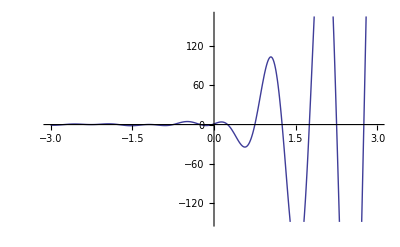

```mathematica
Plot[ Re[zz1[100,z]],{z,-3,3}]
```

```mathematica
Plot[ Re[zz2[100,z]],{z,-3,3}]
```

$Aborted

```mathematica
ff4a[ n_, z_] := Integrate[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
```

```mathematica
ff4a[100,z]
```

-1+LaguerreL[-z,Log[100]]

```mathematica
TestSum[n_,z_,t_]:=Sum[N[Binomial[z,k] (-1)^k (1-Gamma[k,-Log[n]]/Gamma[k])],{k,0,t}]
Grid[Table[{Re[TestSum[n,k,23]],N[LaguerreL[-k,Log[n]]]},{n,10,100,10},{k,-5,5}]]
```

{0.966672,0.966672} | {0.727895,0.727895} | {0.0104133,0.0104133} | {-0.954221,-0.954221} | {-1.30259,-1.30259} | {1.,1.} | {10.,10.} | {33.0259,33.0259} | {82.5612,82.5612} | {178.953,178.953} | {354.26,354.26}
{0.853716,0.853716} | {1.37285,1.37285} | {0.993598,0.993598} | {-0.504259,-0.504259} | {-1.99573,-1.99573} | {1.,1.} | {20.,20.} | {79.9146,79.9146} | {229.573,229.573} | {558.593,558.593} | {1223.71,1223.71}
{0.345442,0.345447} | {1.4452,1.4452} | {1.59103,1.59103} | {-0.018323,-0.0183229} | {-2.4012,-2.4012} | {1.,1.} | {30.,30.} | {132.036,132.036} | {407.594,407.594} | {1053.4,1053.4} | {2433.46,2433.46}
{-0.182647,-0.182608} | {1.31842,1.31842} | {1.97883,1.97883} | {0.426157,0.426157} | {-2.68888,-2.68888} | {1.,1.} | {40.,40.} | {187.555,187.555} | {607.267,607.267} | {1633.79,1633.79} | {3910.39,3910.39}
{-0.66439,-0.664191} | {1.10954,1.10957} | {2.2416,2.2416} | {0.827916,0.827916} | {-2.91202,-2.91202} | {1.,1.} | {50.,50.} | {245.601,245.601} | {823.8,823.8} | {2283.51,2283.51} | {5611.57,5611.57}
{-1.09019,-1.08949} | {0.865209,0.86531} | {2.42308,2.42309} | {1.19314,1.19314} | {-3.09434,-3.09434} | {1.,1.} | {60.,60.} | {305.661,305.661} | {1054.23,1054.23} | {2992.07,2992.07} | {7508.1,7508.1}
{-1.46377,-1.46181} | {0.606799,0.607082} | {2.54836,2.5484} | {1.52786,1.52787} | {-3.2485,-3.2485} | {1.,1.} | {70.,70.} | {367.395,367.395} | {1296.53,1296.53} | {3752.05,3752.05} | {9578.84,9578.84}
{-1.79198,-1.78731} | {0.344902,0.345574} | {2.63302,2.6331} | {1.83702,1.83703} | {-3.38203,-3.38203} | {1.,1.} | {80.,80.} | {430.562,430.562} | {1549.21,1549.21} | {4557.87,4557.87} | {11807.5,11807.5}
{-2.08206,-2.0722} | {0.0849608,0.0863776} | {2.68727,2.68743} | {2.12451,2.12452} | {-3.49981,-3.49981} | {1.,1.} | {90.,90.} | {494.983,494.983} | {1811.14,1811.14} | {5405.17,5405.17} | {14181.2,14181.2}
{-2.34096,-2.32202} | {-0.170259,-0.167536} | {2.71814,2.71845} | {2.39343,2.39346} | {-3.60517,-3.60517} | {1.,1.} | {100.,100.} | {560.517,560.517} | {2081.41,2081.41} | {6290.43,6290.43} | {16689.3,16689.3}

```mathematica
TestSum[n_,z_,t_]:=Sum[N[Binomial[z,k] (-1)^k (1-Gamma[k,-Log[n]]/Gamma[k])],{k,0,t}]
```

```mathematica
TestSum[ 100, 2, 30]
```

560.517-4.41506×10^-14 ⅈ

```mathematica
zz1[n_,k_]:=(-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k])
zz2[n_, k_] :=Integrate[(-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{t,-Log[n],0}]
```

```mathematica
N[zz2[100,2]]
```

361.517

```mathematica
aff2[ n_, z_] := Sum[ Binomial[z,k] (-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k]),{k,0, Infinity}]
```

```mathematica
aff2[100,2,40]
```

200-Gamma[2,-Log[100]]

```mathematica
Limit[ Sum[(j+1) c^j/j ,{j,1, Log[c,n]}],c->1]
```

Limit[(-c+c n+c n LerchPhi[c,1,1+Log[n]/Log[c]]-c^2 n LerchPhi[c,1,1+Log[n]/Log[c]]+Log[1-c]-c Log[1-c])/(-1+c),c→1]

```mathematica
Limit[ Sum[(j+1)(c-1)^2 c^j ,{j,1, Log[c,n]}],c->1]
```

1-n+n Log[n]

```mathematica
Limit[ Sum[(j+1)(j+2)(c-1)^3c^j ,{j,1, Log[c,n]}],c->1]
```

-2+2 n-2 n Log[n]+n Log[n]^2

```mathematica
N[Limit[ Sum[(j+1)(j+2)(j+3)(c-1)^4c^j ,{j,1, Log[c,n]}],c->1]/.n->100]
```

5573.28

```mathematica
Expand[LaguerreL[4, Log[n]]]
```

1-4 Log[n]+3 Log[n]^2-(2 Log[n]^3)/3+Log[n]^4/24

```mathematica
Gamma[ 4, -Log[100.]]
```

-5567.28+2.04539×10^-12 ⅈ

```mathematica
Limit[ Sum[j^z(c-1)^(z+1) c^j ,{j,1, Log[c,n]}],c->1]/.{z->4}
```

24 (-1+n)-24 n Log[n]+12 n Log[n]^2-4 n Log[n]^3+n Log[n]^4

```mathematica
N[Gamma[ 4, -Log[n]]/.n->100]
```

-5567.28+2.04539×10^-12 ⅈ

```mathematica
Limit[ Sum[ c^-j (c-1) ,{j,1, Log[c,n]}],c->1]
```

(-1+n)/n

```mathematica
Limit[ Sum[ c^j (c-1) ,{j,1, Log[c,n]}],c->1]
```

-1+n

```mathematica
Limit[ Sum[ c^j/j (c-1) ,{j,1, Log[c,n]}],c->1]
```

Limit[c n LerchPhi[c,1,1+Log[n]/Log[c]]-c^2 n LerchPhi[c,1,1+Log[n]/Log[c]]+Log[1-c]-c Log[1-c],c→1]